## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## Data reading

```mathematica
saveFolders={"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825","/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800","/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.750"};
```

```mathematica
p0s={3.85,3.775};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000}}
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

{{2,4,10,20,40,60,80,200,500,800,1400,2500,4200,5000,6000,8500,9500},{2,10,20,30,80,100,400,500,2500,2500,3000,7000,10000}}

```mathematica
overlapCRoverlap=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/overlapCRoverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/overlapCRoverlap_N4096_p3.7750_T0.02500000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/overlapCRoverlap_N4096_p3.7750_T0.01600000_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/overlapCRoverlap_N4096_p3.7750_T0.00560000_waitingTime70000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
SISFCRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/SISFCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/SISFCRSISF_N4096_p3.7750_T0.02500000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/SISFCRSISF_N4096_p3.7750_T0.01600000_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/SISFCRSISF_N4096_p3.7750_T0.00560000_waitingTime70000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
CRoverlapMean=Table[Table[Table[Mean[DeleteCases[Table[overlapCRoverlap[[p,T,i,2,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
overlapMean=Table[Table[Table[Mean[DeleteCases[Table[overlapCRoverlap[[p,T,i,1,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
CRSISFMean=Table[Table[Table[Mean[DeleteCases[Table[SISFCRSISF[[p,T,i,2,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,2]]],{i,Length[SISFCRSISF[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
SISFMean=Table[Table[Table[Mean[DeleteCases[Table[SISFCRSISF[[p,T,i,1,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,1]]]-3,{i,Length[SISFCRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
time={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
Flatten[Normal[test2[[4]]]]-test2[[4,1,1]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,-40000.}

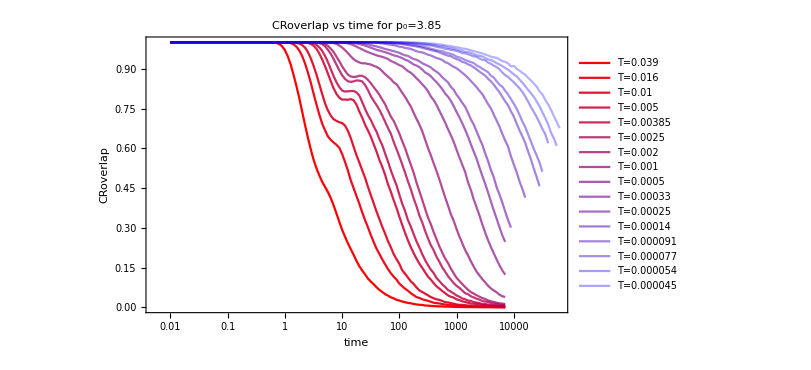
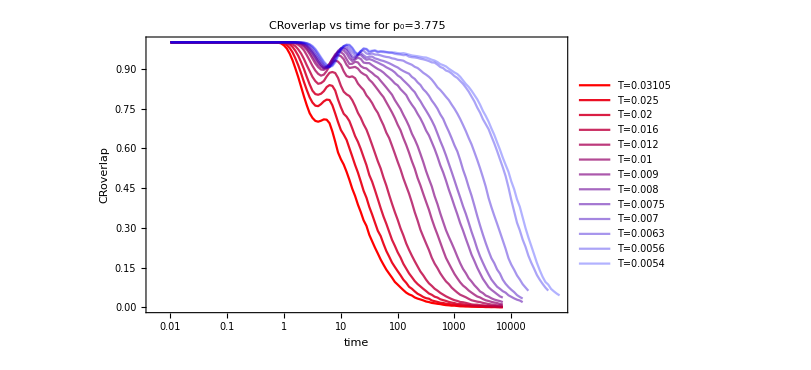

```mathematica
CRoverlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[p,T,rec]]},{rec,Length[CRoverlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRoverlapPlots]
```

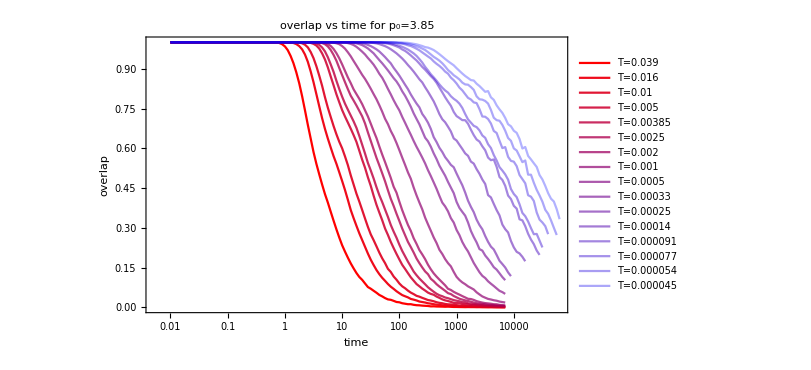
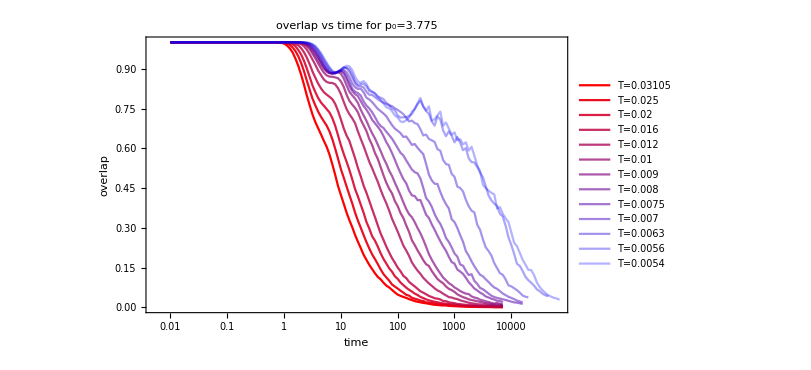

```mathematica
overlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[p,T,rec]]},{rec,Length[overlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[overlapPlots]
```

```mathematica
overlapCRoverlap[[3,10,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
sisfCRSISF[[3,10,1]]
```

<|/firstValue→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{96}],/secondValue→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{96}]|>

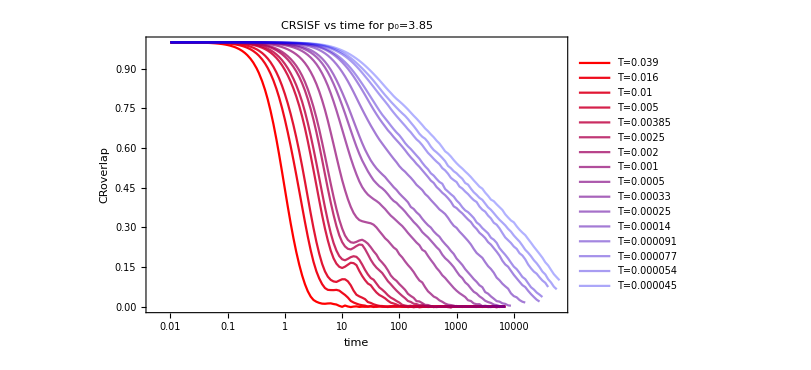
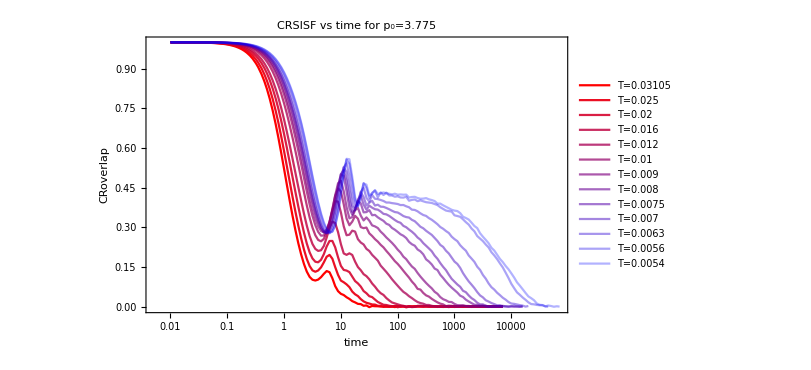

```mathematica
CRSISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRSISFPlots]
```

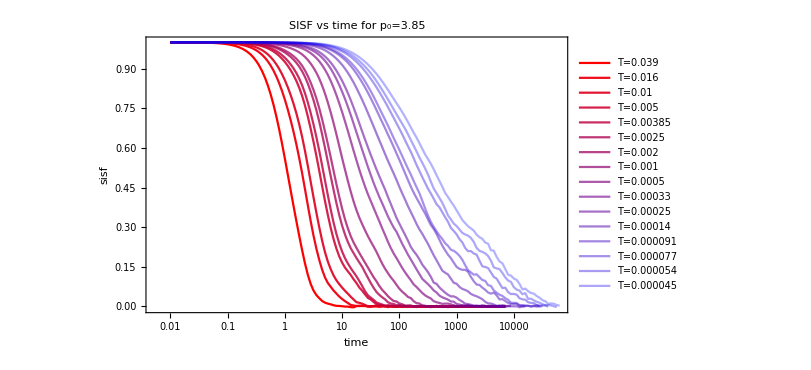
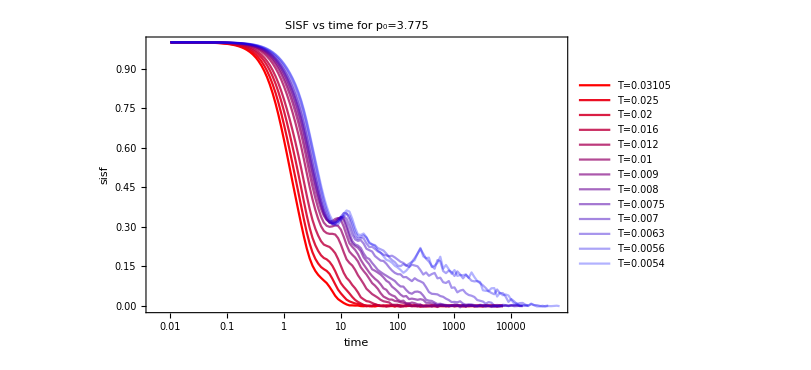

```mathematica
SISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[p,T,rec]]},{rec,Length[SISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","sisf"},ImageSize->600,PlotLabel->"SISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[SISFPlots]
```

```mathematica
fitStartPosNumCRoverlap={{7.504755014358308,12.106781483466941,15.230850791162277,23.175593004078415,28.0384811301167,33.94432141462794,44.305227328893295,71.32074488202053,81.56151599538507,91.44932023141914,121.63461596194325,128.83719634597102,144.4349286332625,155.84779691763205,155.84779691763205,155.84779691763205,155.84779691763205},{12.004706965991755,13.490295078896548,14.584005617164163,16.382073230704947,21.440243968444566,30.27308828495095,32.69334840415353,36.68859493710111,39.618809334670885,43.60309702456088,47.08730608499301,49.878735119872076,49.878735119872076}};
fitStartPosNumCRSISF={{6.903425608507209,14.485562048610838,17.853336669426614,29.82311185277369,34.066272944429734,47.960127626077565,46.171516621994485,52.74068967946601,57.99776784483143,77.1272244581585,77.1272244581585,117.15903635868682,164.9420922998168,160,160,160,160,160},{10.29159442338489312,12.22865353881492,14.530301255613134,18.28672451202404,23.913369623874235,24.37600621876497,34.41553360891785,40.89314245619855,46.7630589870689,48.58995123962369,50.48821468505462,54.510117115927784,56.63966365976017,57.735434834774644}};
```

```mathematica
fitStartPosCRoverlap=Table[Table[Position[time,_?(#>fitStartPosNumCRoverlap[[p,i]]&)][[1,1]],{i,Length[fitStartPosNumCRoverlap[[p]]]}],{p,Length[p0s]}]
fitStartPosCRSISF=Table[Table[Position[time,_?(#>fitStartPosNumCRSISF[[p,i]]&)][[1,1]],{i,Length[fitStartPosNumCRSISF[[p]]]}],{p,Length[p0s]}]
```

{{49,53,55,59,60,62,64,69,70,71,73,74,75,75,75,75,75},{53,54,55,56,58,61,62,63,63,64,65,65,65}}

{{48,55,57,61,62,65,65,66,67,69,69,73,76,76,76,76,76,76},{52,53,55,57,59,59,62,64,65,65,66,66,67,67}}

### fitting CRoverlap

```mathematica
fitsCROverlap=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[p,T,rec]]]},{rec,fitStartPosCRoverlap[[p,T]],Length[CRoverlapMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitsCROverlap[[1,1]]
```

FittedModel[0.989939 ⅇ^(-0.475642 t^0.519386)]

```mathematica
tauCROverlapfits=Table[Table[fitsCROverlap[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{6.77483,22.2632,41.5205,98.0036,134.647,228.734,316.572,830.497,2420.72,4533.12,6984.18,18615.4,39139.,52770.3,102887.,137871.,205724.},{22.2297,35.201,55.6571,94.4109,208.154,373.446,580.285,1088.84,1549.,2492.61,4985.88,12001.6,14784.2}}

```mathematica
CRoverlapFittingPlots=Table[Show[CRoverlapPlots[[p]],Table[LogLinearPlot[fitsCROverlap[[p,T]][x],{x,time[[fitStartPosCRoverlap[[p,T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

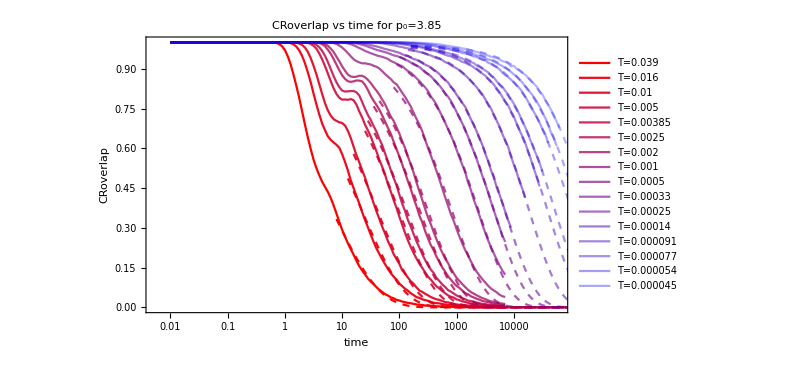
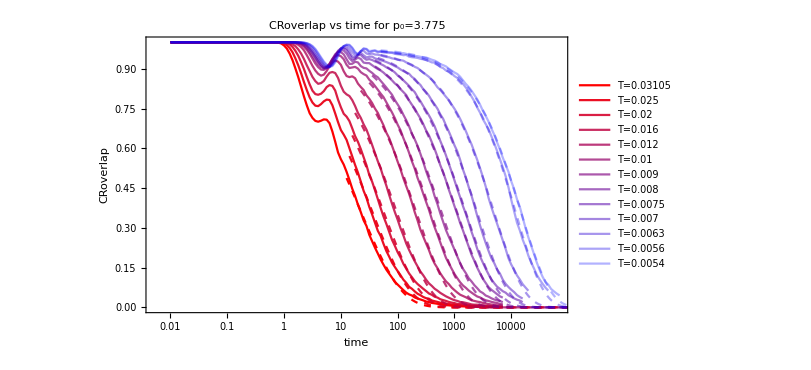

```mathematica
Column[CRoverlapFittingPlots]
```

### fitting CRSISF

```mathematica
fitsCRSISF=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPosCRSISF[[p,T]],Length[CRSISFMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.999>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitsCRSISF[[1]]
```

FittedModel[0.804273 ⅇ^(-0.186921 t^0.824106)]

```mathematica
tauCRSISFfits=Table[Table[fitsCRSISF[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.49265,2.84481,10.1744,22.8496,32.0165,43.9168,66.1196,167.383,363.367,585.215,744.485,1652.78,3013.84,3192.31,4222.84,5157.53,5705.03},{5.94457,6.41409,15.0785,27.6704,54.9392,104.037,174.092,442.466,645.664,1186.6,2420.23,6244.64,7453.97}}

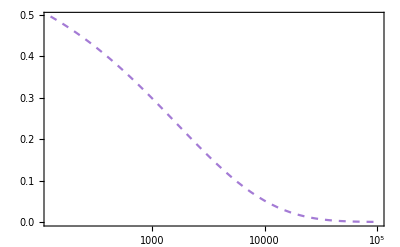
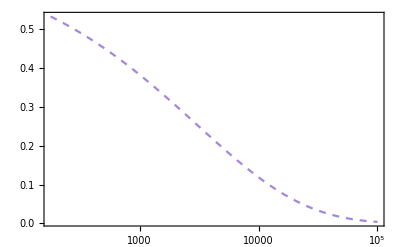
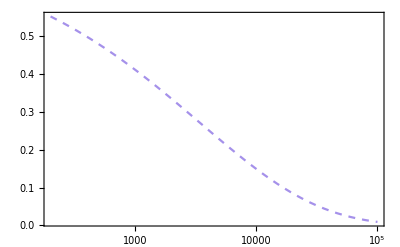
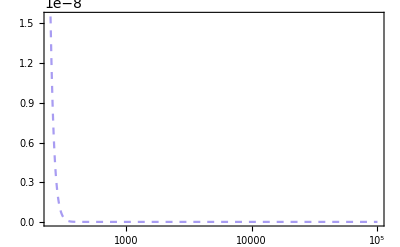
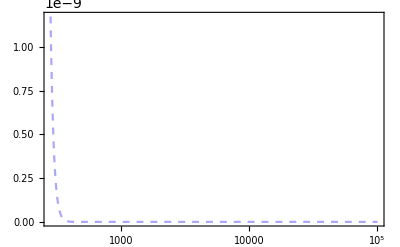
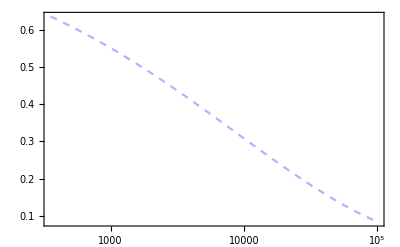
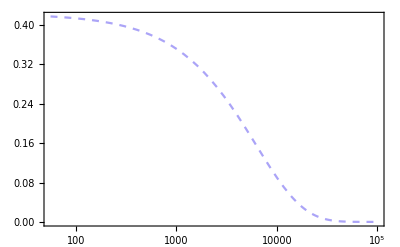
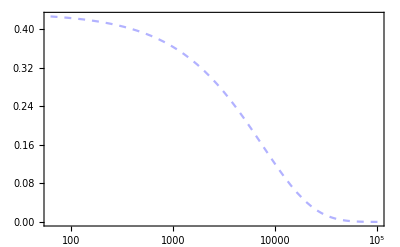

```mathematica
Table[Table[LogLinearPlot[fitsCRSISF[[p,T]][x],{x,time[[fitStartPosCRSISF[[p,T]]]],100000},PlotRange->All,PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,12,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

```mathematica
CRSISFFittingPlots=Table[Show[CRSISFPlots[[p]],Table[LogLinearPlot[fitsCRSISF[[p,T]][x],{x,time[[fitStartPosCRSISF[[p,T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

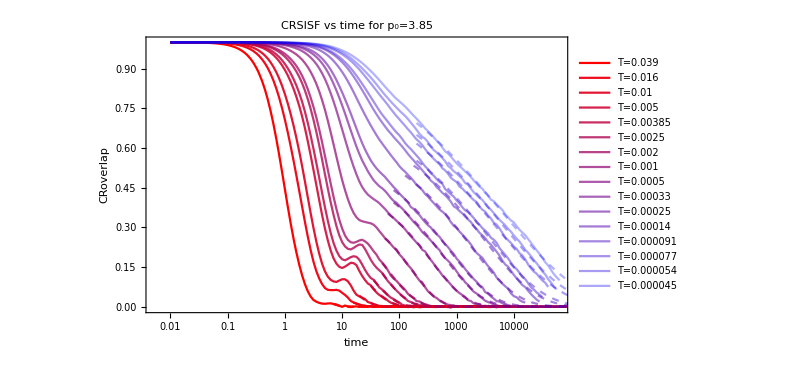
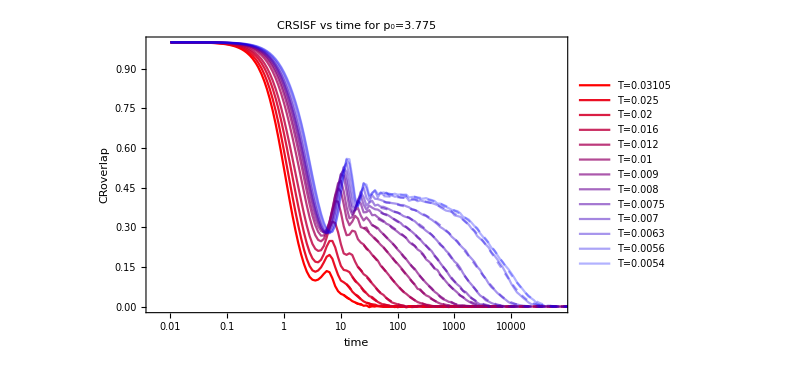

```mathematica
Column[CRSISFFittingPlots]
```

### fitting SISF

```mathematica
fitsSISF=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[p,T,rec]]]},{rec,fitStartPosCRSISF[[p,T]],Length[SISFMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
tauSISFfits=Table[Table[fitsSISF[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.14206,1.41367,4.59726,8.52174,7.45864,11.5078,16.9221,57.7582,33.6789,57.1643,75.7619,148.5,250.27,298.555,570.761,790.794,1195.39},{2.41641,2.15086,4.65021,5.05511,5.53238,7.27438,13.5534,7.48454,89.5165,182.754,708.793,3515.17,4386.43}}

```mathematica
SISFFittingPlots=Table[Show[SISFPlots[[p]],Table[LogLinearPlot[fitsSISF[[p,T]][x],{x,time[[fitStartPosCRSISF[[p,T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

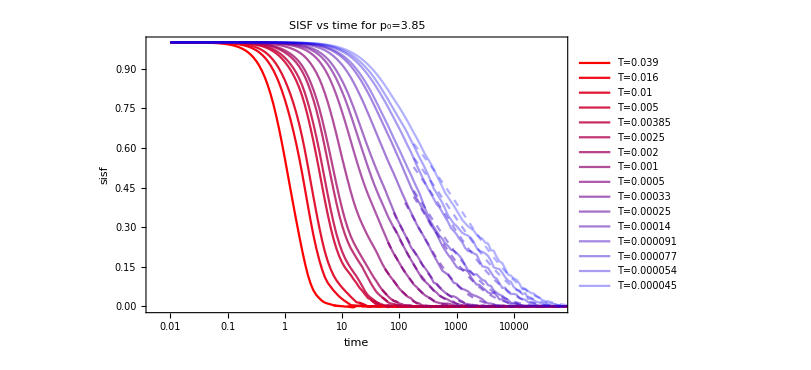
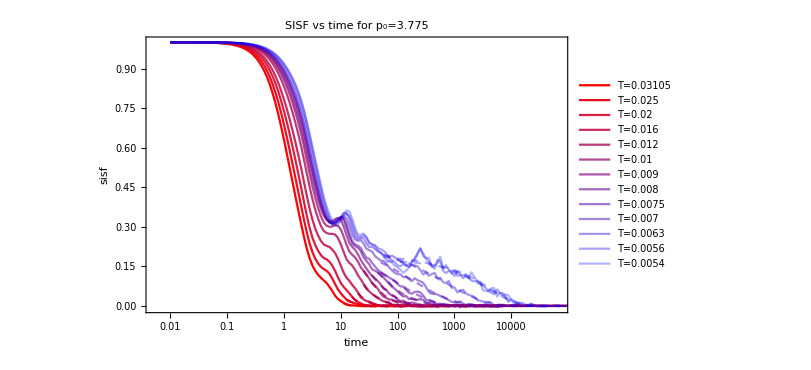

```mathematica
Column[SISFFittingPlots]
```

### fitting overlap

```mathematica
fitsoverlap=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[p,T,rec]]]},{rec,fitStartPosCRoverlap[[p,T]],Length[overlapMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
tauoverlapfits=Table[Table[fitsoverlap[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{4.86865,13.4036,22.1023,44.8011,58.6472,90.6202,121.694,274.308,722.926,1304.36,2015.23,5008.94,11117.2,14155.4,24274.2,35806.8,52586.3},{10.7503,16.5315,24.1668,37.445,73.9943,113.214,158.941,290.858,460.378,995.12,2564.15,8147.07,9770.99}}

```mathematica
overlapFittingPlots=Table[Show[overlapPlots[[p]],Table[LogLinearPlot[fitsoverlap[[p,T]][x],{x,time[[fitStartPosCRoverlap[[p,T]]+7]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

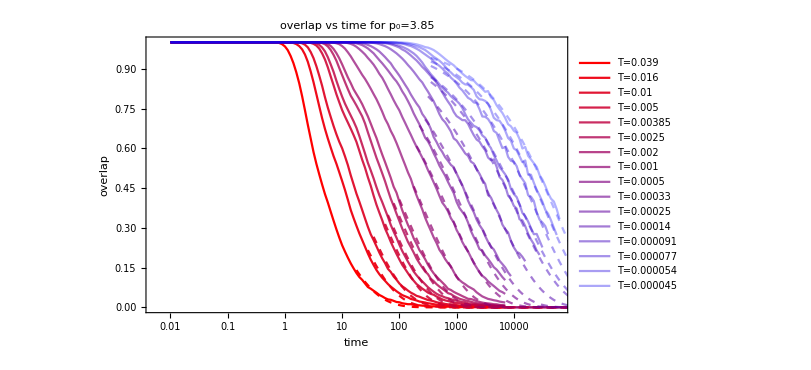
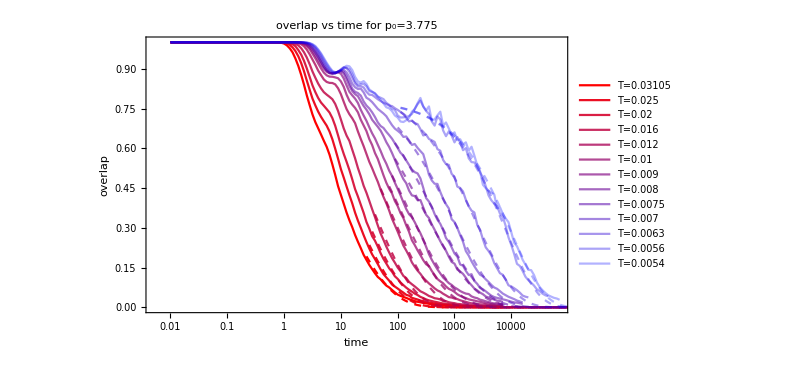

```mathematica
Column[overlapFittingPlots]
```

#### Tau Alphas

```mathematica
tauAlphafitingPlot=Table[ListLogPlot[{Table[{1/temperatures[[p,T]],tauCROverlapfits[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauCRSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauoverlapfits[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" τα vs 1/T",Joined->True,PlotRange->All],{p,Length[p0s]}];
```

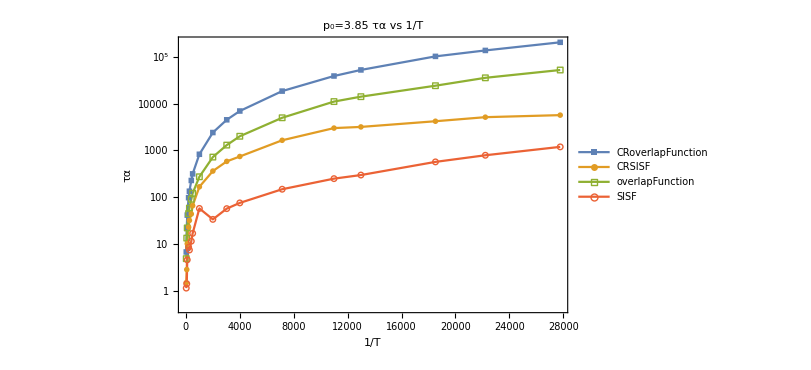
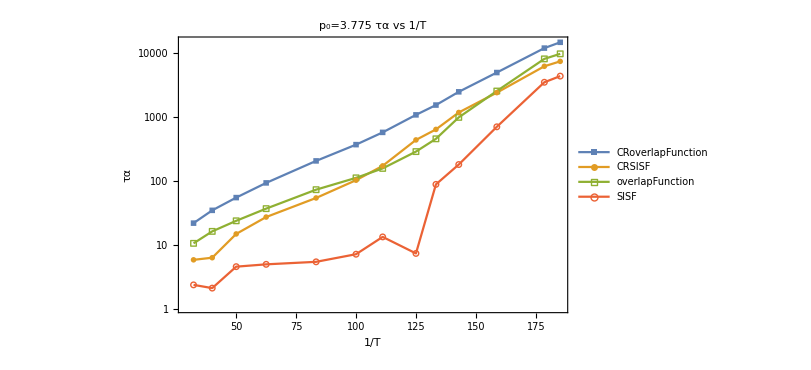

```mathematica
Column[tauAlphafitingPlot]
```

```mathematica
tauTables=Table[Prepend[Table[{temperatures[[p,T]],tauCRSISFfits[[p,T]],tauCROverlapfits[[p,T]],tauoverlapfits[[p,T]],tauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}],{p,Length[p0s]}];
```

```mathematica
ToString[NumberForm[p0s[[1]],{5,3}]]
```

3.825

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>"_Over10conf.csv",tauTables[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.850_Over10conf.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.775_Over10conf.csv}

### log-log plots for croverlap and cr sisf

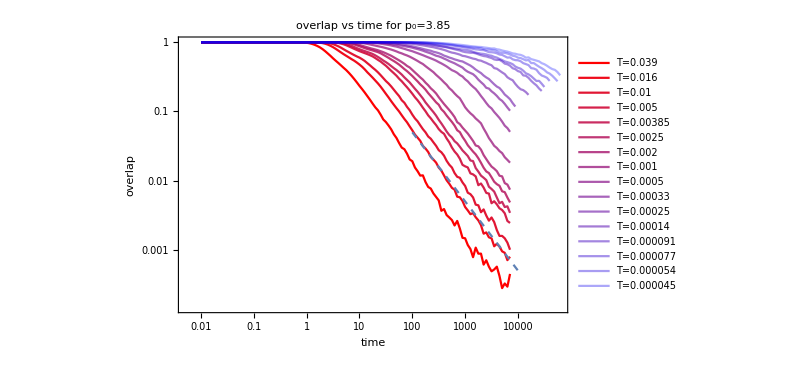
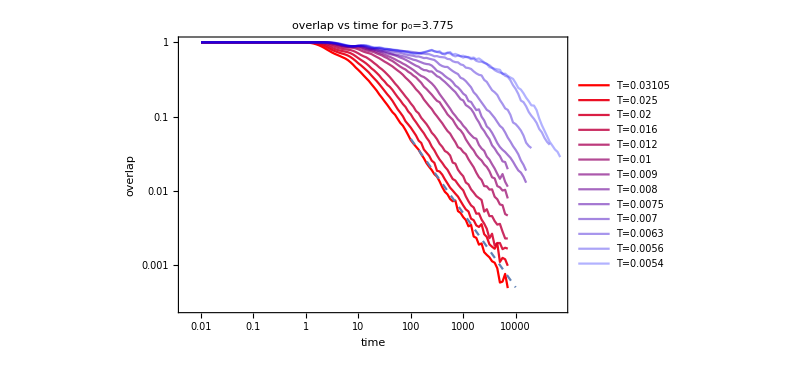

```mathematica
overlapLogLogPlots=Table[
Show[ListLogLogPlot[Table[Table[{time[[rec]],overlapMean[[p,T,rec]]},{rec,Length[overlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],LogLogPlot[5x^-1,{x,100,10000},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[overlapLogLogPlots]
```

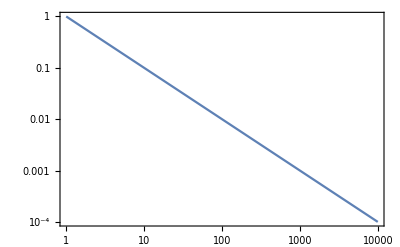

```mathematica
LogLogPlot[x^-1,{x,1,10000}]
```

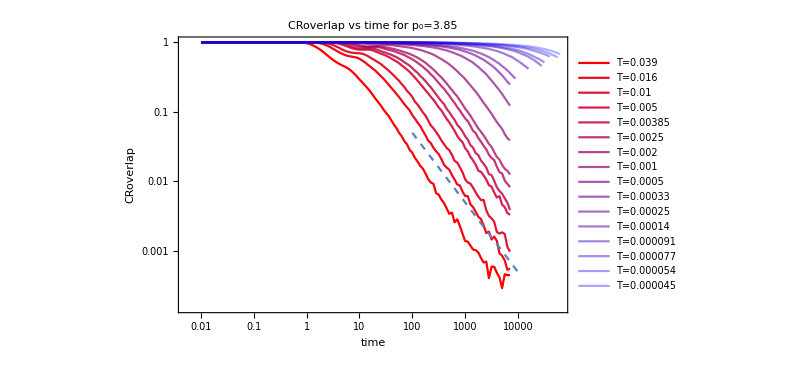
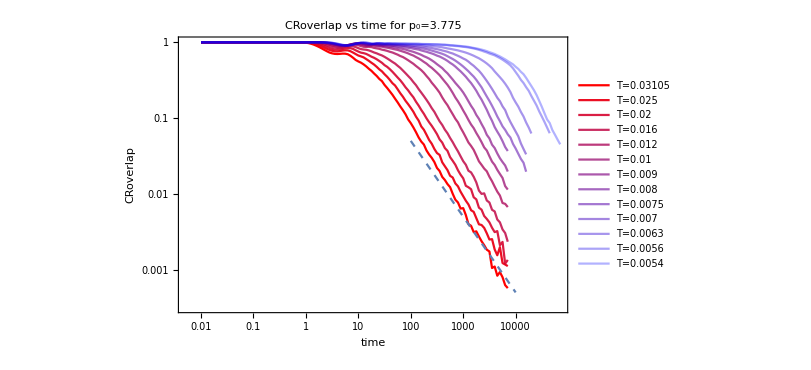

```mathematica
CRoverlapLogLogPlots=Table[
Show[ListLogLogPlot[Table[Table[{time[[rec]],CRoverlapMean[[p,T,rec]]},{rec,Length[CRoverlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],LogLogPlot[5x^-1,{x,100,10000},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[CRoverlapLogLogPlots]
```

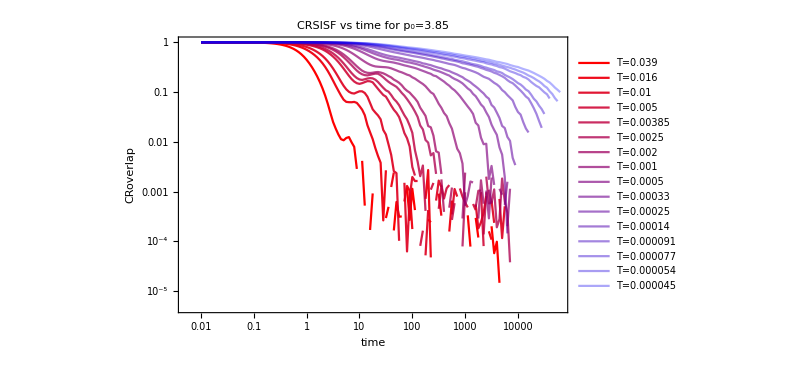
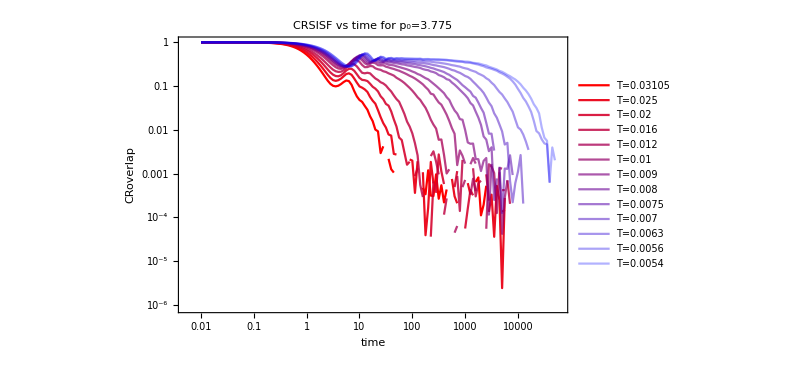

```mathematica
CRSISFLogLogPlots=Table[
ListLogLogPlot[Table[Table[{time[[rec]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRSISFLogLogPlots]
```